Testing Spatial Audio on a Single Plane - 2D

## Determining Time Delays based on Ear Location [Complete]

Graphical Visualization

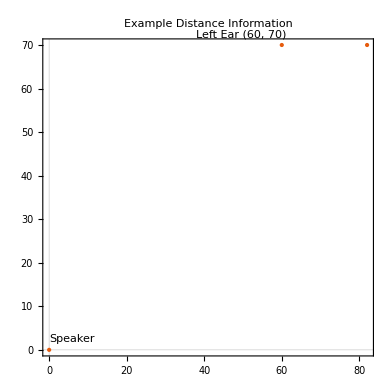

```mathematica
ListPlot[{
Labeled[{0,0},"Speaker"],
Labeled[{60,70}, "Left Ear (60, 70)"],
Labeled[{82,70}, "Right Ear (62, 70)"]
},
PlotTheme->"Scientific",
(*PlotRange->{{0,100},{0,100}},*)
PlotStyle->PointSize[Large],
ScalingFunctions->{Identity,Identity}, 
AspectRatio->1,
PlotRangePadding->10,
PlotLabel->"Example Distance Information"]
```

Assigning Attributes

```mathematica
distanceLeftEar = Quantity[√(60.^2+70.^2),"centimeters"]
distanceRightEar = Quantity[√(62.^2+70.^2), "centimeters"]
(*Angle Between Speaker and X-axis when connected as Right Triangle with Ear*)
thetaLeftEar =Quantity[ArcTan[70./60.] ,"radians"]
thetaRightEar =Quantity[ArcTan[70./62.], "radians"]
```

92.1954 cm

93.5094 cm

0.86217 rad

0.84593 rad

Speed of Sound

```mathematica
speedOfSound =StandardAtmosphereData[Quantity[0, "feet"],"SoundSpeed"]
```

340.29 m/s

Determining Delays

```mathematica
delayLeftEar=distanceLeftEar/speedOfSound
delayRightEar = distanceRightEar / speedOfSound
```

0.00270932 s

0.00274793 s

## Working with Audio Functions to Channel Delay [Complete]

```mathematica
sampleAudio=Import["/Users/shubhamkumar/Downloads/prenks/Serene Queen - LDR.mp3"]
```

```mathematica
(*Doesn't Work, Stereo not split into Mono for each Channel*)
AudioChannelSeparate[sampleAudio]
```

{,}

Visualizing Audio and Trimming For Faster Processing

-Graphics-

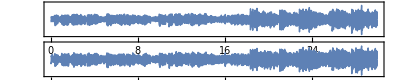

2

```mathematica
sampleAudioTrimmed = AudioTrim[sampleAudio, {10,40}]
Spectrogram[sampleAudioTrimmed]
AudioPlot[sampleAudioTrimmed]
AudioChannels[sampleAudioTrimmed]
```

Panning Test

```mathematica
leftAudio = AudioPan[sampleAudioTrimmed,-1.]
rightAudio = AudioPan[sampleAudioTrimmed, 1.]
```

```mathematica
AudioChannelCombine[{leftAudio, rightAudio}]
```

Delaying Audio For Each Channel

```mathematica
delayedLeftAudio = AudioDelay[leftAudio,delayLeftEar]
delayedRightAudio= AudioDelay[rightAudio,delayRightEar]
(*Making Sure Delay Worked*)
Duration@{delayedLeftAudio, delayedRightAudio, leftAudio, rightAudio}
```

{30.0027 s,30.0027 s,30. s,30. s}

```mathematica
spatial2dAudioTrimmed = AudioChannelCombine[{delayedRightAudio, delayedLeftAudio}]
```

Checking Differences

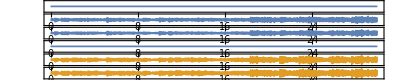

{4,2}

```mathematica
AudioPlot@{spatial2dAudioTrimmed, sampleAudioTrimmed}
AudioChannels@{spatial2dAudioTrimmed, sampleAudioTrimmed}
```

## Functional Implementation of Single Plane 2D Audio with Delay and Simple Attenuation [Complete] [Performance][ISQ Law dB Attenuation]

Combining Processes from Previous Sections + Adding in Audio Amplification

```mathematica
PlotPoint2dAudio[speakerPoint_, leftEar_, rightEar_]:=
Module[{speakerPointLoc=speakerPoint, leftEarPointLoc=leftEar, rightEarPointLoc=rightEar},
(*Bruh why do arrays start at 1*)
(*Print[speakerPointLoc[[0]]];*)
ListPlot[{
Labeled[{speakerPointLoc[[1]], speakerPointLoc[[2]]},"Speaker"],
Labeled[{leftEarPointLoc[[1]], leftEarPointLoc[[2]]}, "Left Ear"],
Labeled[{rightEarPointLoc[[1]], rightEarPointLoc[[2]]}, "Right Ear"]
},
PlotTheme->"Scientific",
(*PlotRange->{{0,100},{0,100}},*)
PlotStyle->PointSize[Large],
ScalingFunctions->{Identity,Identity}, 
AspectRatio->1,
PlotRangePadding->10,
PlotLabel->"Distance Information"]
]
```

Implementing Inverse Square Law [Experimenting]

```mathematica
Point2dAudioV1[file_, speakerPoint_, leftEar_, rightEar_, amplificationProportion_, trimStart_, trimEnd_]:=
Module[{fileLoc=file, speakerPointLoc=speakerPoint, leftEarPointLoc=leftEar, rightEarPointLoc=rightEar, k=amplificationProportion, t1=trimStart, t2=trimEnd},
(*Trimming Raw Audio & Separating Audio for each Channel*)
rawAudioData = Import[fileLoc];
trimmedRawAudioData = AudioNormalize[AudioTrim[rawAudioData,{t1, t2}]];
leftAudioData = AudioPan[trimmedRawAudioData,-1.];
rightAudioData = AudioPan[trimmedRawAudioData, 1.];

(*Calculating Delays*)
leftEarDistanceFromSpeaker = Quantity[√((leftEarPointLoc[[1]]-speakerPointLoc[[1]])^2.+(leftEarPointLoc[[2]]-speakerPointLoc[[2]])^2.), "centimeters"];
rightEarDistanceFromSpeaker = Quantity[√((rightEarPointLoc[[1]]-speakerPointLoc[[1]])^2.+(rightEarPointLoc[[2]]-speakerPointLoc[[2]])^2.), "centimeters"];
speedOfSound = StandardAtmosphereData[Quantity[0, "feet"],"SoundSpeed"];
leftEarAudioDelay = leftEarDistanceFromSpeaker/speedOfSound;
rightEarAudioDelay = rightEarDistanceFromSpeaker/speedOfSound;

(*Debug*)
(*Print["Left Ear Audio Distance:"]; Print[leftEarDistanceFromSpeaker];
Print["Right Ear Audio Distance:"]; Print[rightEarDistanceFromSpeaker];
Print["Left Ear Audio Delay:"]; Print[leftEarAudioDelay];
Print["Right Ear Audio Delay:"]; Print[rightEarAudioDelay];*)

(*Audio Delaying & Trash Attenuation*)
(*leftEarAudioDelayedData = If[QuantityMagnitude[leftEarDistanceFromSpeaker] ≠ 0, 
AudioAmplify[AudioDelay[leftAudioData, leftEarAudioDelay], QuantityMagnitude[k/leftEarDistanceFromSpeaker]], 
leftAudioData];
rightEarAudioDelayedData = If[QuantityMagnitude[rightEarDistanceFromSpeaker]≠ 0, 
AudioAmplify[AudioDelay[rightAudioData, rightEarAudioDelay], QuantityMagnitude[k/rightEarDistanceFromSpeaker]], 
rightAudioData];*)

(*Audio Delaying & Less Trash Attenuation*)

(*Mixing to Generate Final Sound*)
AudioNormalize[AudioChannelCombine[{leftEarAudioDelayedData, rightEarAudioDelayedData}]]
]
```

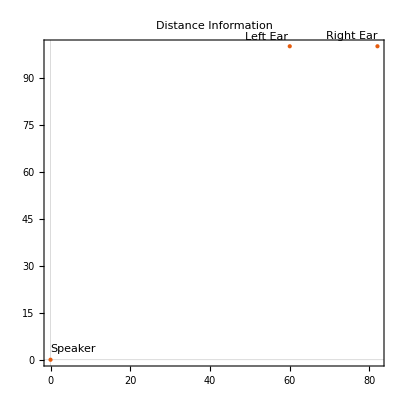

```mathematica
PlotPoint2dAudio[{0,0},{60,100},{82,100}]
```

Function Unit Tests

```mathematica
delayTest = Point2dAudioV1["/Users/shubhamkumar/Downloads/prenks/Thunder - LDR.mp3",{0,0},{60,100},{82,100}, 100, 0, 30]
```

Left channel is indeed louder than the right

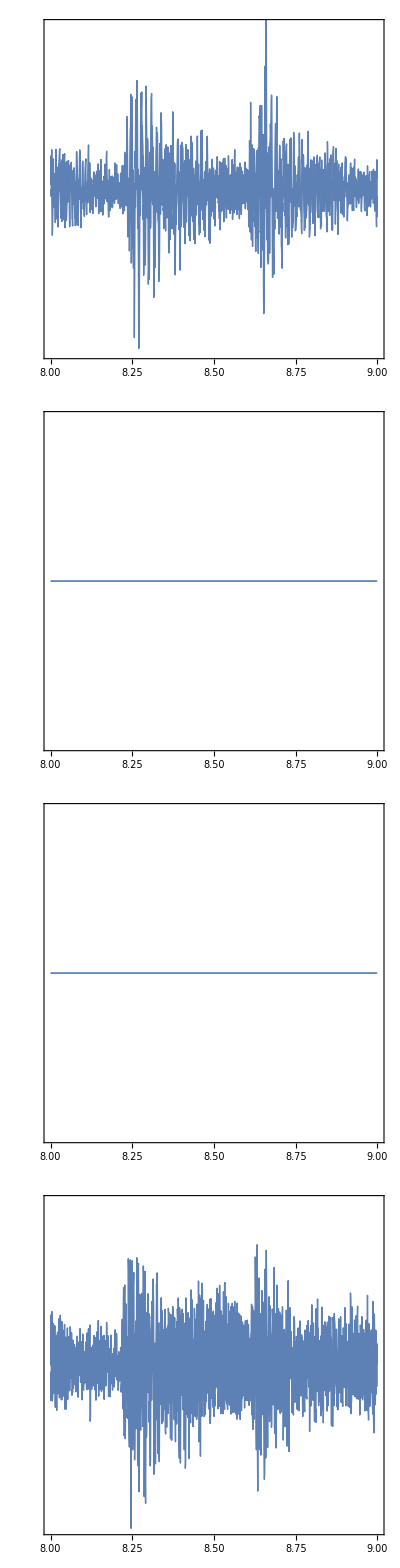

-Graphics-

4

```mathematica
AudioPlot[delayTest, PlotRange->{{8,9},{-0.8, 0.8}}]
Spectrogram[delayTest]
AudioChannels[delayTest]
```

```mathematica
delayTestLoudness =AudioLoudness[delayTest]
```

TimeSeries[…]

Speaker and Ears are all at the same location

```mathematica
(*Lmao don't run this - fixed it, its fine now*)
sanityTest = Point2dAudioV1["/Users/shubhamkumar/Downloads/prenks/Thunder - LDR.mp3",{0,0},{0,0},{0,0}, 100, 0, 30]
```

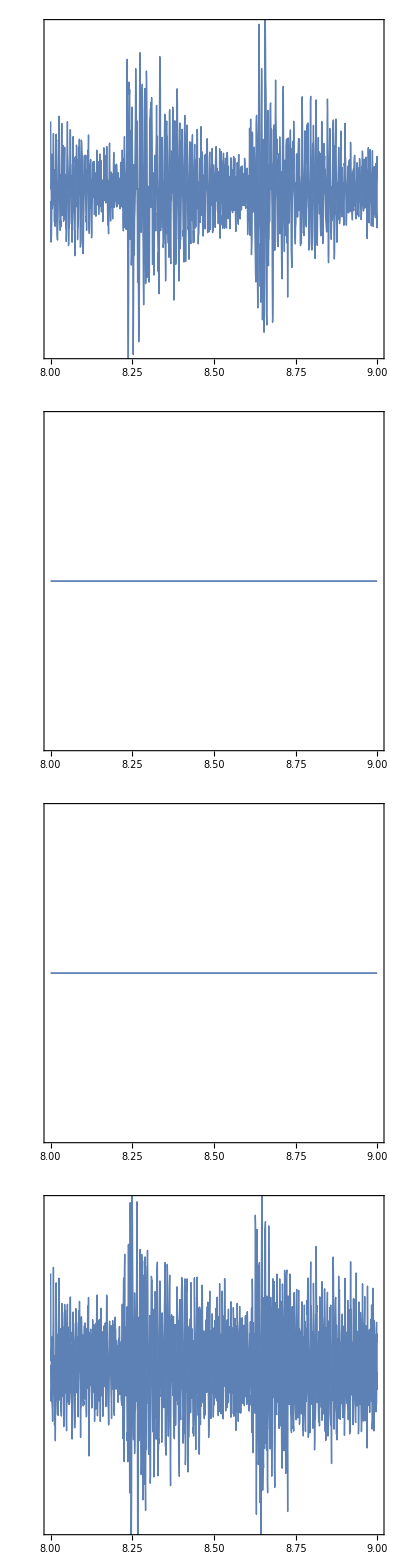

-Graphics-

4

```mathematica
AudioPlot[sanityTest, PlotRange->{{8,9},{-0.8,0.8}}]
Spectrogram[sanityTest]
AudioChannels[sanityTest]
```

```mathematica
sanityTestLoudness = AudioLoudness[sanityTest]
```

TimeSeries[…]

Comparing With Raw Audio - Can’t Quite Tell a Difference but the Audio Plot Shows that there is

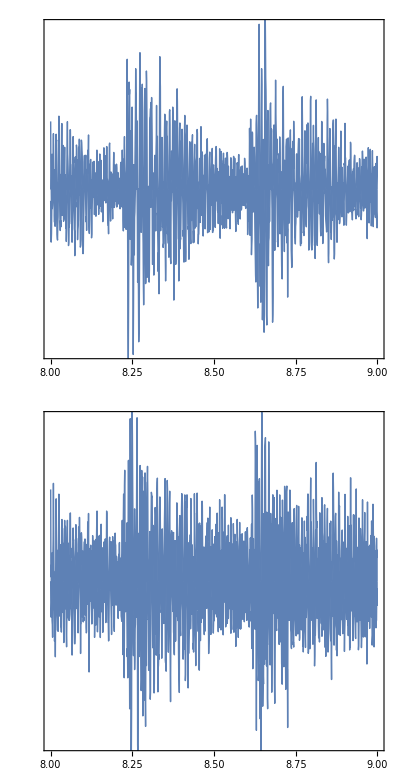

```mathematica
rawAudioComparison=AudioNormalize[AudioTrim[Import["/Users/shubhamkumar/Downloads/prenks/Thunder - LDR.mp3"],{0,30}]]
AudioPlot[rawAudioComparison, PlotRange-> {{8,9},{-0.8, 0.8}}]
```

```mathematica
rawAudioLoudness =AudioLoudness[rawAudioComparison]
```

TimeSeries[…]

Comparing Loudness

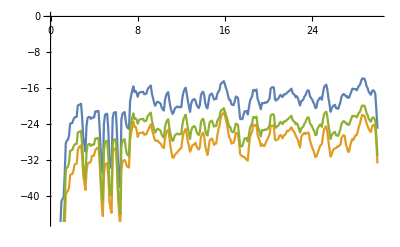

```mathematica
ListLinePlot@{rawAudioLoudness, delayTestLoudness, sanityTestLoudness}
```

## Extend Function to Understand that the Head is an Obstacle [In Progress Section: PDE TDS][Using Acoustics]

## Moving Speaker in a 2D Plane [Canceled][Performance][Using Acoustics]

Testing

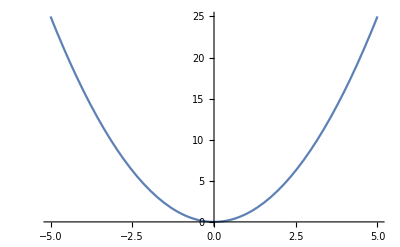

{25.,23.7656,22.5625,21.3906,20.25,19.1406,18.0625,17.0156,16.,15.0156,14.0625,13.1406,12.25,11.3906,10.5625,9.76563,9.,8.26563,7.5625,6.89063,6.25,5.64063,5.0625,4.51563,4.,3.51563,3.0625,2.64063,2.25,1.89063,1.5625,1.26563,1.,0.765625,0.5625,0.390625,0.25,0.140625,0.0625,0.015625,0.,0.015625,0.0625,0.140625,0.25,0.390625,0.5625,0.765625,1.,1.26563,1.5625,1.89063,2.25,2.64063,3.0625,3.51563,4.,4.51563,5.0625,5.64063,6.25,6.89063,7.5625,8.26563,9.,9.76563,10.5625,11.3906,12.25,13.1406,14.0625,15.0156,16.,17.0156,18.0625,19.1406,20.25,21.3906,22.5625,23.7656,25.}

81

```mathematica
Plot[x^2,{x,-5,5}]
locationVals =Table[y^2,{y,-5.,5.,0.125}]
Length[locationVals]
```

Can’t Implement this for my life

```mathematica
(*PlotPath2dAudio[speakerPath_, range_, leftEar_, rightEar_]:=
Module[{speakerPointLoc=speakerPath, rangeLoc=range, leftEarPointLoc=leftEar, rightEarPointLoc=rightEar},
(*Bruh why do arrays start at 1*)
(*Print[speakerPointLoc[[0]]];*)
ListPlot[Echo@Join[{
Legended[{leftEarPointLoc[[1]], leftEarPointLoc[[2]]}, "Left Ear"],
Legended[{rightEarPointLoc[[1]], rightEarPointLoc[[2]]}, "Right Ear"]},
Table[{Sin[n], Sin[2 n]}, {n, 10}]],
PlotTheme->"Scientific",
(*PlotRange->{{0,100},{0,100}},*)
PlotStyle->PointSize[Large],
ScalingFunctions->{Identity,Identity}, 
AspectRatio->1,
PlotRangePadding->10,
PlotLabel->"Distance Information"]
]*)
```

```mathematica
(*PlotPath2dAudio[{0,0},{1,1},{2,2}, {3,3}]*)
```

Visualizing Points

```mathematica
points = Table[{4.n, 100.*Sin[ n]}, {n,0,8Pi, Pi/100}]
Length@points
```

{{0.,0.},{0.125664,3.14108},{0.251327,6.27905},{0.376991,9.41083},{0.502655,12.5333},{0.628319,15.6434},{0.753982,18.7381},{0.879646,21.8143},{1.00531,24.869},{1.13097,27.8991},{1.25664,30.9017},{1.3823,33.8738},{1.50796,36.8125},{1.63363,39.7148},{1.75929,42.5779},{1.88496,45.399},{2.01062,48.1754},{2.13628,50.9041},{2.26195,53.5827},{2.38761,56.2083},{2.51327,58.7785},{2.63894,61.2907},{2.7646,63.7424},{2.89027,66.1312},{3.01593,68.4547},{3.14159,70.7107},{3.26726,72.8969},{3.39292,75.0111},{3.51858,77.0513},{3.64425,79.0155},{3.76991,80.9017},{3.89557,82.7081},{4.02124,84.4328},{4.1469,86.0742},{4.27257,87.6307},{4.39823,89.1007},{4.52389,90.4827},{4.64956,91.7755},{4.77522,92.9776},{4.90088,94.0881},{5.02655,95.1057},{5.15221,96.0294},{5.27788,96.8583},{5.40354,97.5917},{5.5292,98.2287},{5.65487,98.7688},{5.78053,99.2115},{5.90619,99.5562},{6.03186,99.8027},{6.15752,99.9507},{6.28319,100.},{6.40885,99.9507},{6.53451,99.8027},{6.66018,99.5562},{6.78584,99.2115},{6.9115,98.7688},{7.03717,98.2287},{7.16283,97.5917},{7.28849,96.8583},{7.41416,96.0294},{7.53982,95.1057},{7.66549,94.0881},{7.79115,92.9776},{7.91681,91.7755},{8.04248,90.4827},{8.16814,89.1007},{8.2938,87.6307},{8.41947,86.0742},{8.54513,84.4328},{8.6708,82.7081},{8.79646,80.9017},{8.92212,79.0155},{9.04779,77.0513},{9.17345,75.0111},{9.29911,72.8969},{9.42478,70.7107},{9.55044,68.4547},{9.67611,66.1312},{9.80177,63.7424},{9.92743,61.2907},{10.0531,58.7785},{10.1788,56.2083},{10.3044,53.5827},{10.4301,50.9041},{10.5558,48.1754},{10.6814,45.399},{10.8071,42.5779},{10.9327,39.7148},{11.0584,36.8125},{11.1841,33.8738},{11.3097,30.9017},{11.4354,27.8991},{11.5611,24.869},{11.6867,21.8143},{11.8124,18.7381},{11.9381,15.6434},{12.0637,12.5333},{12.1894,9.41083},{12.315,6.27905},{12.4407,3.14108},{12.5664,0.},{12.692,-3.14108},{12.8177,-6.27905},{12.9434,-9.41083},{13.069,-12.5333},{13.1947,-15.6434},{13.3204,-18.7381},{13.446,-21.8143},{13.5717,-24.869},{13.6973,-27.8991},{13.823,-30.9017},{13.9487,-33.8738},{14.0743,-36.8125},{14.2,-39.7148},{14.3257,-42.5779},{14.4513,-45.399},{14.577,-48.1754},{14.7027,-50.9041},{14.8283,-53.5827},{14.954,-56.2083},{15.0796,-58.7785},{15.2053,-61.2907},{15.331,-63.7424},{15.4566,-66.1312},{15.5823,-68.4547},{15.708,-70.7107},{15.8336,-72.8969},{15.9593,-75.0111},{16.085,-77.0513},{16.2106,-79.0155},{16.3363,-80.9017},{16.4619,-82.7081},{16.5876,-84.4328},{16.7133,-86.0742},{16.8389,-87.6307},{16.9646,-89.1007},{17.0903,-90.4827},{17.2159,-91.7755},{17.3416,-92.9776},{17.4673,-94.0881},{17.5929,-95.1057},{17.7186,-96.0294},{17.8442,-96.8583},{17.9699,-97.5917},{18.0956,-98.2287},{18.2212,-98.7688},{18.3469,-99.2115},{18.4726,-99.5562},{18.5982,-99.8027},{18.7239,-99.9507},{18.8496,-100.},{18.9752,-99.9507},{19.1009,-99.8027},{19.2265,-99.5562},{19.3522,-99.2115},{19.4779,-98.7688},{19.6035,-98.2287},{19.7292,-97.5917},{19.8549,-96.8583},{19.9805,-96.0294},{20.1062,-95.1057},{20.2319,-94.0881},{20.3575,-92.9776},{20.4832,-91.7755},{20.6088,-90.4827},{20.7345,-89.1007},{20.8602,-87.6307},{20.9858,-86.0742},{21.1115,-84.4328},{21.2372,-82.7081},{21.3628,-80.9017},{21.4885,-79.0155},{21.6142,-77.0513},{21.7398,-75.0111},{21.8655,-72.8969},{21.9911,-70.7107},{22.1168,-68.4547},{22.2425,-66.1312},{22.3681,-63.7424},{22.4938,-61.2907},{22.6195,-58.7785},{22.7451,-56.2083},{22.8708,-53.5827},{22.9965,-50.9041},{23.1221,-48.1754},{23.2478,-45.399},{23.3734,-42.5779},{23.4991,-39.7148},{23.6248,-36.8125},{23.7504,-33.8738},{23.8761,-30.9017},{24.0018,-27.8991},{24.1274,-24.869},{24.2531,-21.8143},{24.3788,-18.7381},{24.5044,-15.6434},{24.6301,-12.5333},{24.7558,-9.41083},{24.8814,-6.27905},{25.0071,-3.14108},{25.1327,0.},{25.2584,3.14108},{25.3841,6.27905},{25.5097,9.41083},{25.6354,12.5333},{25.7611,15.6434},{25.8867,18.7381},{26.0124,21.8143},{26.1381,24.869},{26.2637,27.8991},{26.3894,30.9017},{26.515,33.8738},{26.6407,36.8125},{26.7664,39.7148},{26.892,42.5779},{27.0177,45.399},{27.1434,48.1754},{27.269,50.9041},{27.3947,53.5827},{27.5204,56.2083},{27.646,58.7785},{27.7717,61.2907},{27.8973,63.7424},{28.023,66.1312},{28.1487,68.4547},{28.2743,70.7107},{28.4,72.8969},{28.5257,75.0111},{28.6513,77.0513},{28.777,79.0155},{28.9027,80.9017},{29.0283,82.7081},{29.154,84.4328},{29.2796,86.0742},{29.4053,87.6307},{29.531,89.1007},{29.6566,90.4827},{29.7823,91.7755},{29.908,92.9776},{30.0336,94.0881},{30.1593,95.1057},{30.285,96.0294},{30.4106,96.8583},{30.5363,97.5917},{30.6619,98.2287},{30.7876,98.7688},{30.9133,99.2115},{31.0389,99.5562},{31.1646,99.8027},{31.2903,99.9507},{31.4159,100.},{31.5416,99.9507},{31.6673,99.8027},{31.7929,99.5562},{31.9186,99.2115},{32.0442,98.7688},{32.1699,98.2287},{32.2956,97.5917},{32.4212,96.8583},{32.5469,96.0294},{32.6726,95.1057},{32.7982,94.0881},{32.9239,92.9776},{33.0496,91.7755},{33.1752,90.4827},{33.3009,89.1007},{33.4265,87.6307},{33.5522,86.0742},{33.6779,84.4328},{33.8035,82.7081},{33.9292,80.9017},{34.0549,79.0155},{34.1805,77.0513},{34.3062,75.0111},{34.4319,72.8969},{34.5575,70.7107},{34.6832,68.4547},{34.8088,66.1312},{34.9345,63.7424},{35.0602,61.2907},{35.1858,58.7785},{35.3115,56.2083},{35.4372,53.5827},{35.5628,50.9041},{35.6885,48.1754},{35.8142,45.399},{35.9398,42.5779},{36.0655,39.7148},{36.1911,36.8125},{36.3168,33.8738},{36.4425,30.9017},{36.5681,27.8991},{36.6938,24.869},{36.8195,21.8143},{36.9451,18.7381},{37.0708,15.6434},{37.1965,12.5333},{37.3221,9.41083},{37.4478,6.27905},{37.5734,3.14108},{37.6991,0.},{37.8248,-3.14108},{37.9504,-6.27905},{38.0761,-9.41083},{38.2018,-12.5333},{38.3274,-15.6434},{38.4531,-18.7381},{38.5788,-21.8143},{38.7044,-24.869},{38.8301,-27.8991},{38.9557,-30.9017},{39.0814,-33.8738},{39.2071,-36.8125},{39.3327,-39.7148},{39.4584,-42.5779},{39.5841,-45.399},{39.7097,-48.1754},{39.8354,-50.9041},{39.9611,-53.5827},{40.0867,-56.2083},{40.2124,-58.7785},{40.338,-61.2907},{40.4637,-63.7424},{40.5894,-66.1312},{40.715,-68.4547},{40.8407,-70.7107},{40.9664,-72.8969},{41.092,-75.0111},{41.2177,-77.0513},{41.3434,-79.0155},{41.469,-80.9017},{41.5947,-82.7081},{41.7204,-84.4328},{41.846,-86.0742},{41.9717,-87.6307},{42.0973,-89.1007},{42.223,-90.4827},{42.3487,-91.7755},{42.4743,-92.9776},{42.6,-94.0881},{42.7257,-95.1057},{42.8513,-96.0294},{42.977,-96.8583},{43.1027,-97.5917},{43.2283,-98.2287},{43.354,-98.7688},{43.4796,-99.2115},{43.6053,-99.5562},{43.731,-99.8027},{43.8566,-99.9507},{43.9823,-100.},{44.108,-99.9507},{44.2336,-99.8027},{44.3593,-99.5562},{44.485,-99.2115},{44.6106,-98.7688},{44.7363,-98.2287},{44.8619,-97.5917},{44.9876,-96.8583},{45.1133,-96.0294},{45.2389,-95.1057},{45.3646,-94.0881},{45.4903,-92.9776},{45.6159,-91.7755},{45.7416,-90.4827},{45.8673,-89.1007},{45.9929,-87.6307},{46.1186,-86.0742},{46.2442,-84.4328},{46.3699,-82.7081},{46.4956,-80.9017},{46.6212,-79.0155},{46.7469,-77.0513},{46.8726,-75.0111},{46.9982,-72.8969},{47.1239,-70.7107},{47.2496,-68.4547},{47.3752,-66.1312},{47.5009,-63.7424},{47.6265,-61.2907},{47.7522,-58.7785},{47.8779,-56.2083},{48.0035,-53.5827},{48.1292,-50.9041},{48.2549,-48.1754},{48.3805,-45.399},{48.5062,-42.5779},{48.6319,-39.7148},{48.7575,-36.8125},{48.8832,-33.8738},{49.0088,-30.9017},{49.1345,-27.8991},{49.2602,-24.869},{49.3858,-21.8143},{49.5115,-18.7381},{49.6372,-15.6434},{49.7628,-12.5333},{49.8885,-9.41083},{50.0142,-6.27905},{50.1398,-3.14108},{50.2655,0.},{50.3911,3.14108},{50.5168,6.27905},{50.6425,9.41083},{50.7681,12.5333},{50.8938,15.6434},{51.0195,18.7381},{51.1451,21.8143},{51.2708,24.869},{51.3965,27.8991},{51.5221,30.9017},{51.6478,33.8738},{51.7734,36.8125},{51.8991,39.7148},{52.0248,42.5779},{52.1504,45.399},{52.2761,48.1754},{52.4018,50.9041},{52.5274,53.5827},{52.6531,56.2083},{52.7788,58.7785},{52.9044,61.2907},{53.0301,63.7424},{53.1557,66.1312},{53.2814,68.4547},{53.4071,70.7107},{53.5327,72.8969},{53.6584,75.0111},{53.7841,77.0513},{53.9097,79.0155},{54.0354,80.9017},{54.1611,82.7081},{54.2867,84.4328},{54.4124,86.0742},{54.538,87.6307},{54.6637,89.1007},{54.7894,90.4827},{54.915,91.7755},{55.0407,92.9776},{55.1664,94.0881},{55.292,95.1057},{55.4177,96.0294},{55.5434,96.8583},{55.669,97.5917},{55.7947,98.2287},{55.9203,98.7688},{56.046,99.2115},{56.1717,99.5562},{56.2973,99.8027},{56.423,99.9507},{56.5487,100.},{56.6743,99.9507},{56.8,99.8027},{56.9257,99.5562},{57.0513,99.2115},{57.177,98.7688},{57.3027,98.2287},{57.4283,97.5917},{57.554,96.8583},{57.6796,96.0294},{57.8053,95.1057},{57.931,94.0881},{58.0566,92.9776},{58.1823,91.7755},{58.308,90.4827},{58.4336,89.1007},{58.5593,87.6307},{58.685,86.0742},{58.8106,84.4328},{58.9363,82.7081},{59.0619,80.9017},{59.1876,79.0155},{59.3133,77.0513},{59.4389,75.0111},{59.5646,72.8969},{59.6903,70.7107},{59.8159,68.4547},{59.9416,66.1312},{60.0673,63.7424},{60.1929,61.2907},{60.3186,58.7785},{60.4442,56.2083},{60.5699,53.5827},{60.6956,50.9041},{60.8212,48.1754},{60.9469,45.399},{61.0726,42.5779},{61.1982,39.7148},{61.3239,36.8125},{61.4496,33.8738},{61.5752,30.9017},{61.7009,27.8991},{61.8265,24.869},{61.9522,21.8143},{62.0779,18.7381},{62.2035,15.6434},{62.3292,12.5333},{62.4549,9.41083},{62.5805,6.27905},{62.7062,3.14108},{62.8319,0.},{62.9575,-3.14108},{63.0832,-6.27905},{63.2088,-9.41083},{63.3345,-12.5333},{63.4602,-15.6434},{63.5858,-18.7381},{63.7115,-21.8143},{63.8372,-24.869},{63.9628,-27.8991},{64.0885,-30.9017},{64.2142,-33.8738},{64.3398,-36.8125},{64.4655,-39.7148},{64.5911,-42.5779},{64.7168,-45.399},{64.8425,-48.1754},{64.9681,-50.9041},{65.0938,-53.5827},{65.2195,-56.2083},{65.3451,-58.7785},{65.4708,-61.2907},{65.5965,-63.7424},{65.7221,-66.1312},{65.8478,-68.4547},{65.9734,-70.7107},{66.0991,-72.8969},{66.2248,-75.0111},{66.3504,-77.0513},{66.4761,-79.0155},{66.6018,-80.9017},{66.7274,-82.7081},{66.8531,-84.4328},{66.9788,-86.0742},{67.1044,-87.6307},{67.2301,-89.1007},{67.3557,-90.4827},{67.4814,-91.7755},{67.6071,-92.9776},{67.7327,-94.0881},{67.8584,-95.1057},{67.9841,-96.0294},{68.1097,-96.8583},{68.2354,-97.5917},{68.3611,-98.2287},{68.4867,-98.7688},{68.6124,-99.2115},{68.738,-99.5562},{68.8637,-99.8027},{68.9894,-99.9507},{69.115,-100.},{69.2407,-99.9507},{69.3664,-99.8027},{69.492,-99.5562},{69.6177,-99.2115},{69.7434,-98.7688},{69.869,-98.2287},{69.9947,-97.5917},{70.1203,-96.8583},{70.246,-96.0294},{70.3717,-95.1057},{70.4973,-94.0881},{70.623,-92.9776},{70.7487,-91.7755},{70.8743,-90.4827},{71.,-89.1007},{71.1257,-87.6307},{71.2513,-86.0742},{71.377,-84.4328},{71.5026,-82.7081},{71.6283,-80.9017},{71.754,-79.0155},{71.8796,-77.0513},{72.0053,-75.0111},{72.131,-72.8969},{72.2566,-70.7107},{72.3823,-68.4547},{72.508,-66.1312},{72.6336,-63.7424},{72.7593,-61.2907},{72.8849,-58.7785},{73.0106,-56.2083},{73.1363,-53.5827},{73.2619,-50.9041},{73.3876,-48.1754},{73.5133,-45.399},{73.6389,-42.5779},{73.7646,-39.7148},{73.8903,-36.8125},{74.0159,-33.8738},{74.1416,-30.9017},{74.2673,-27.8991},{74.3929,-24.869},{74.5186,-21.8143},{74.6442,-18.7381},{74.7699,-15.6434},{74.8956,-12.5333},{75.0212,-9.41083},{75.1469,-6.27905},{75.2726,-3.14108},{75.3982,0.},{75.5239,3.14108},{75.6496,6.27905},{75.7752,9.41083},{75.9009,12.5333},{76.0265,15.6434},{76.1522,18.7381},{76.2779,21.8143},{76.4035,24.869},{76.5292,27.8991},{76.6549,30.9017},{76.7805,33.8738},{76.9062,36.8125},{77.0319,39.7148},{77.1575,42.5779},{77.2832,45.399},{77.4088,48.1754},{77.5345,50.9041},{77.6602,53.5827},{77.7858,56.2083},{77.9115,58.7785},{78.0372,61.2907},{78.1628,63.7424},{78.2885,66.1312},{78.4142,68.4547},{78.5398,70.7107},{78.6655,72.8969},{78.7911,75.0111},{78.9168,77.0513},{79.0425,79.0155},{79.1681,80.9017},{79.2938,82.7081},{79.4195,84.4328},{79.5451,86.0742},{79.6708,87.6307},{79.7965,89.1007},{79.9221,90.4827},{80.0478,91.7755},{80.1734,92.9776},{80.2991,94.0881},{80.4248,95.1057},{80.5504,96.0294},{80.6761,96.8583},{80.8018,97.5917},{80.9274,98.2287},{81.0531,98.7688},{81.1788,99.2115},{81.3044,99.5562},{81.4301,99.8027},{81.5557,99.9507},{81.6814,100.},{81.8071,99.9507},{81.9327,99.8027},{82.0584,99.5562},{82.1841,99.2115},{82.3097,98.7688},{82.4354,98.2287},{82.5611,97.5917},{82.6867,96.8583},{82.8124,96.0294},{82.938,95.1057},{83.0637,94.0881},{83.1894,92.9776},{83.315,91.7755},{83.4407,90.4827},{83.5664,89.1007},{83.692,87.6307},{83.8177,86.0742},{83.9434,84.4328},{84.069,82.7081},{84.1947,80.9017},{84.3203,79.0155},{84.446,77.0513},{84.5717,75.0111},{84.6973,72.8969},{84.823,70.7107},{84.9487,68.4547},{85.0743,66.1312},{85.2,63.7424},{85.3257,61.2907},{85.4513,58.7785},{85.577,56.2083},{85.7026,53.5827},{85.8283,50.9041},{85.954,48.1754},{86.0796,45.399},{86.2053,42.5779},{86.331,39.7148},{86.4566,36.8125},{86.5823,33.8738},{86.708,30.9017},{86.8336,27.8991},{86.9593,24.869},{87.0849,21.8143},{87.2106,18.7381},{87.3363,15.6434},{87.4619,12.5333},{87.5876,9.41083},{87.7133,6.27905},{87.8389,3.14108},{87.9646,0.},{88.0903,-3.14108},{88.2159,-6.27905},{88.3416,-9.41083},{88.4672,-12.5333},{88.5929,-15.6434},{88.7186,-18.7381},{88.8442,-21.8143},{88.9699,-24.869},{89.0956,-27.8991},{89.2212,-30.9017},{89.3469,-33.8738},{89.4726,-36.8125},{89.5982,-39.7148},{89.7239,-42.5779},{89.8495,-45.399},{89.9752,-48.1754},{90.1009,-50.9041},{90.2265,-53.5827},{90.3522,-56.2083},{90.4779,-58.7785},{90.6035,-61.2907},{90.7292,-63.7424},{90.8549,-66.1312},{90.9805,-68.4547},{91.1062,-70.7107},{91.2319,-72.8969},{91.3575,-75.0111},{91.4832,-77.0513},{91.6088,-79.0155},{91.7345,-80.9017},{91.8602,-82.7081},{91.9858,-84.4328},{92.1115,-86.0742},{92.2372,-87.6307},{92.3628,-89.1007},{92.4885,-90.4827},{92.6142,-91.7755},{92.7398,-92.9776},{92.8655,-94.0881},{92.9911,-95.1057},{93.1168,-96.0294},{93.2425,-96.8583},{93.3681,-97.5917},{93.4938,-98.2287},{93.6195,-98.7688},{93.7451,-99.2115},{93.8708,-99.5562},{93.9965,-99.8027},{94.1221,-99.9507},{94.2478,-100.},{94.3734,-99.9507},{94.4991,-99.8027},{94.6248,-99.5562},{94.7504,-99.2115},{94.8761,-98.7688},{95.0018,-98.2287},{95.1274,-97.5917},{95.2531,-96.8583},{95.3788,-96.0294},{95.5044,-95.1057},{95.6301,-94.0881},{95.7557,-92.9776},{95.8814,-91.7755},{96.0071,-90.4827},{96.1327,-89.1007},{96.2584,-87.6307},{96.3841,-86.0742},{96.5097,-84.4328},{96.6354,-82.7081},{96.7611,-80.9017},{96.8867,-79.0155},{97.0124,-77.0513},{97.138,-75.0111},{97.2637,-72.8969},{97.3894,-70.7107},{97.515,-68.4547},{97.6407,-66.1312},{97.7664,-63.7424},{97.892,-61.2907},{98.0177,-58.7785},{98.1434,-56.2083},{98.269,-53.5827},{98.3947,-50.9041},{98.5203,-48.1754},{98.646,-45.399},{98.7717,-42.5779},{98.8973,-39.7148},{99.023,-36.8125},{99.1487,-33.8738},{99.2743,-30.9017},{99.4,-27.8991},{99.5257,-24.869},{99.6513,-21.8143},{99.777,-18.7381},{99.9026,-15.6434},{100.028,-12.5333},{100.154,-9.41083},{100.28,-6.27905},{100.405,-3.14108},{100.531,0.}}

801

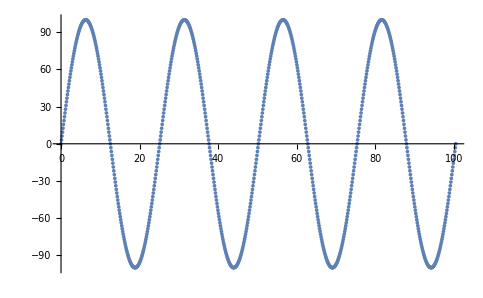

```mathematica
ListPlot[points, ScalingFunctions->{Identity,Identity}]
```

```mathematica
Path2dAudioV1[file_, speakerPath_, leftEar_, rightEar_, amplificationProportion_, duration_]:=
Module[{fileLoc=file, speakerPointLoc=speakerPath, leftEarPointLoc=leftEar, rightEarPointLoc=rightEar, k=amplificationProportion, durationLoc=duration},
subtrimLengths = durationLoc/Length[speakerPath];
AudioJoin[MapIndexed[Point2dAudioV1[file, #1, leftEar, rightEar, amplificationProportion, 30+(First[#2]-1)*subtrimLengths, 30+First[#2]*subtrimLengths]&, speakerPath]]
]
```

Very Time Consuming Computation - How can I speed this up?

```mathematica
(*out = Path2dAudioV1["/Users/shubhamkumar/Downloads/prenks/Thunder - LDR.mp3", points, {39,-100}, {61, -100}, 100, 10]*)
```

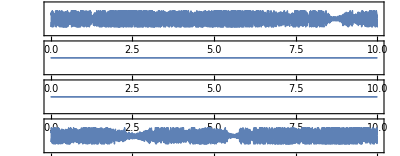

```mathematica
(*AudioPlot[out, PlotRange->{{0,10},{-2,2}}]*)
```

```mathematica
AudioNormalize[out]
```

## Doppler Effect in a 2D Plane [Canceled][Attenuation Needed][Figure out how to use Acoustics]

Source and Observer are on the Same Line, Observer is Stationary, Minimal Implementation

```mathematica
rawFrequency = Quantity[500,"Hz"]
velocitySource = Quantity[5, "m/s"]
```

500 Hz

5 m/s

```mathematica
AudioGenerator[{"Sin",100}]
```

```mathematica
sourcePath = Table[n,{n,0,25,0.25}];
Length@sourcePath;
(*Head@sourcePath
Head@{-1*#&/@sourcePath[[51;;101]]}*)
negPosi=Reverse[-1*#&/@sourcePath[[1;;50]]];
posPosi=sourcePath[[1;;51]];
sourcePath =Join[negPosi, posPosi]
Length@sourcePath
(*sourcePath = Join[sourcePath[1;;50],{-1*#&/@sourcePath[[51;;101]]}]*)
```

{-12.25,-12.,-11.75,-11.5,-11.25,-11.,-10.75,-10.5,-10.25,-10.,-9.75,-9.5,-9.25,-9.,-8.75,-8.5,-8.25,-8.,-7.75,-7.5,-7.25,-7.,-6.75,-6.5,-6.25,-6.,-5.75,-5.5,-5.25,-5.,-4.75,-4.5,-4.25,-4.,-3.75,-3.5,-3.25,-3.,-2.75,-2.5,-2.25,-2.,-1.75,-1.5,-1.25,-1.,-0.75,-0.5,-0.25,0.,0.,0.25,0.5,0.75,1.,1.25,1.5,1.75,2.,2.25,2.5,2.75,3.,3.25,3.5,3.75,4.,4.25,4.5,4.75,5.,5.25,5.5,5.75,6.,6.25,6.5,6.75,7.,7.25,7.5,7.75,8.,8.25,8.5,8.75,9.,9.25,9.5,9.75,10.,10.25,10.5,10.75,11.,11.25,11.5,11.75,12.,12.25,12.5}

101

```mathematica
DopplerFormula[actualFrequency_, sourceVelocity_, observerVelocity_, soundVelocity_, observerPosition_]:=
Module[{actualFreqLoc=actualFrequency, vS=sourceVelocity, vO=observerVelocity, v=soundVelocity, poi=observerPosition},
(*Calculating Perceived Frequency*)
{If[observerPosition ≠ 0, 1/observerPosition, 5], actualFreqLoc*((v+vO)/(v-(-Sign[poi]*vS)))}
]
```

```mathematica
percFreqs=DopplerFormula [rawFrequency, velocitySource, 0, StandardAtmosphereData[Quantity[0, "feet"],"SoundSpeed"],#]&/@ sourcePath
```

{507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,500. Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz}

```mathematica
rawOut = AudioJoin[AudioGenerator[{"Sin", #},0.1]&/@percFreqs]
```

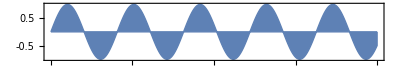

```mathematica
AudioPlot[rawOut, PlotRange->{2,2.01}]
```

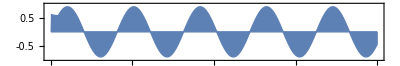

```mathematica
gaussOut = MeanFilter[rawOut,10]
AudioPlot[gaussOut, PlotRange->{2,2.01}]
```

Attenuation

## Testing PDE TIME DOMAIN Stuff *All above obsolete if this works [Working]

Tutorial Implementation

```mathematica
Ω=RegionUnion[Disk[{0,1/4},3/5,{0,π}],Rectangle[{-(23/200),0},{-(17/200),1/4}],Rectangle[{17/200,0},{23/200,1/4}]];
```

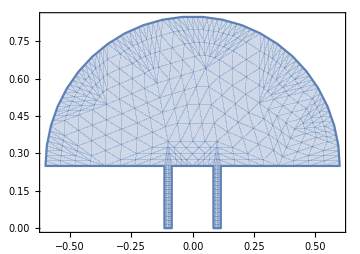

```mathematica
RegionPlot[Ω,Sequence[AspectRatio->Automatic,ImageSize->Medium], PlotPoints->10]
```

```mathematica
trbc=NeumannValue[-((I ω)/(ρ c))*p[x,y]+(2 I ω)/(ρ c)*5,y==0];
```

```mathematica
tabc=NeumannValue[-((I ω)/(ρ c))*p[x,y],y>1/4];
```

```mathematica
cair=QuantityMagnitude[ThermodynamicData["Air","SoundSpeed"]];
pair=QuantityMagnitude[ThermodynamicData["Air","Density"]];
```

```mathematica
λ=1/10;
f=cair/λ;
```

```mathematica
pde={-((ω^2 p[x,y])/(c^2 ρ))+Inactive[Div][({{-(1/ρ),0},{0,-(1/ρ)}}.Inactive[Grad][p[x,y],{x,y}]),{x,y}]==tabc+trbc}/.{c->cair,ρ->pair,ω->2 π f};
```

```mathematica
pde
```

{-3277.37 p[x,y]+({{-0.830168,0},{0,-0.830168}}.p[x,y]{x,y}Inactive){x,y}Inactive==NeumannValue[(0.+521.61 ⅈ)-(0.+52.161 ⅈ) p[x,y],y==0]+NeumannValue[(0.-52.161 ⅈ) p[x,y],y>1/4]}

```mathematica
pfun=NDSolveValue[pde,p,{x,y}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->1/40000}}}];
```

```mathematica
pfun[0,0.6]
```

1.4629-0.665524 ⅈ

```mathematica
ContourPlot[Re[pfun[x,y]*Exp[I ω 0.001]/.{ω->2 π f}],{x,y}∈Ω,Sequence[PlotRange->{-7.5,7.5},ColorFunction->ColorData[{"LightTemperatureMap",{-3,3}}],ColorFunctionScaling->False,Contours->Apply[Range,Flatten[{{-3,3},(1/8) Abs[Apply[Subtract,{-3,3}]]}]],PlotPoints->41,AspectRatio->Automatic,Frame->False,Axes->False,ImageSize->Medium]]
```

-Graphics-

Random Testing Irrelevant

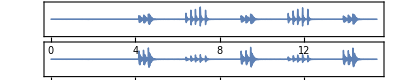

```mathematica
AudioPlot[Import["/Users/shubhamkumar/Desktop/orens.ogg"]]
```

Extending Tutorial to New Bound Conditions and Regions

```mathematica
Clear["Global`*"]
```

```mathematica
(*OΩ=RegionDifference[RegionUnion[Rectangle[{0,0},{0.25,0.25}],Rectangle[{0.25,0.05},{0.4,0.0625}],Disk[{0,0.25},0.125,{0,2Pi}]],Disk[{0,0.25},0.025]];*)
OΩ = RegionDifference[RegionDifference[Rectangle[{0,0},{0.25,0.25}],Disk[{0.1,0.1}, 0.025]],Disk[{0.25,0},0.0125]];
(*RegionUnion[Disk[{0,1/4},3/5,{0,π}],Rectangle[{-(23/200),0},{-(17/200),1/4}],Rectangle[{17/200,0},{23/200,1/4}]];*)
(*p=RegionUnion[Disk[{0,1/4},3/5,{0,π}],Rectangle[{-(23/200),0},{-(17/200),1/4}],Rectangle[{17/200,0},{23/200,1/4}]];*)
```

```mathematica
RegionPlot[OΩ,Sequence[AspectRatio->Automatic,ImageSize->Medium], PlotStyle->"Scientific"]
```

-Graphics-

```mathematica
(*Absorbing Boundary Condition*)
(*Gabc=NeumannValue[-((I ω)/(ρ c))*p[x,y],y>0];
Grbc = NeumannValue[-((I ω)/(ρ c))*p[x,y]+(2 I ω)/(ρ c)*5,x>0.2];
Gabc2 = NeumannValue[-((I ω)/(ρ c))*p[x,y],0.025>x>-0.025&&0.275>y>0.225];*)
```

```mathematica
Gabc = NeumannValue[-((I ω)/(ρ c))*p[x,y],y≥0.0125&&x≤ 0.2375];
Grbc = NeumannValue[-((I ω)/(ρ c))*p[x,y]+(2 I ω)/(ρ c)*5,0.0125>y≥0&&0.25≥x> 0.2375];
```

```mathematica
(*IDK how to do booleans clearly*)
0<1<=1&&2<=2
```

True

```mathematica
(*Subscript[Γ,RBC]=NeumannValue[-((I ω)/(ρ c))*p[x,y]+(2 I ω)/(ρ c)*5,y==0];*)
```

```mathematica
(*Params*)
Cair=QuantityMagnitude[ThermodynamicData["Air","SoundSpeed"]];
Pair=QuantityMagnitude[ThermodynamicData["Air","Density"]];
```

```mathematica
(*Sound Attributes*)
Oλ=1/10;
Of=Cair/Oλ;
```

```mathematica
Opde={-((ω^2 p[x,y])/(c^2 ρ))+Inactive[Div][({{-(1/ρ),0},{0,-(1/ρ)}}.Inactive[Grad][p[x,y],{x,y}]),{x,y}]==Gabc+Grbc}/.{c->Cair,ρ->Pair,ω->2 π Of}
```

{-3277.37 p[x,y]+({{-0.830168,0},{0,-0.830168}}.p[x,y]{x,y}Inactive){x,y}Inactive==NeumannValue[(0.+521.61 ⅈ)-(0.+52.161 ⅈ) p[x,y],0.0125>y≥0&&0.25≥x>0.2375]+NeumannValue[(0.-52.161 ⅈ) p[x,y],y≥0.0125&&x≤0.2375]}

```mathematica
OΩ
```

BooleanRegion[#1&&!#2&&!#3&,{Rectangle[{0,0},{0.25,0.25}],Disk[{0.1,0.1},0.025],Disk[{0.25,0},0.0125]}]

```mathematica
pfun=NDSolveValue[Opde,p,{x,y}∈OΩ,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->1/40000}}}];
```

```mathematica
pfun
```

InterpolatingFunction[…]

```mathematica
ResourceFunction["ComputationalEssayTemplate"][]
```

t2nun_shm30FrontEndObject[LinkObject["t2nun_shm", 3, 1]]30Untitled-3

```mathematica
ContourPlot[Re[pfun[x,y]*Exp[I ω 0]/.{ω->2 π Of}],{x,y}∈OΩ,Sequence[PlotRange->{-7.5,7.5},ColorFunction->ColorData[{"LightTemperatureMap",{-3,3}}],ColorFunctionScaling->False,Contours->Apply[Range,Flatten[{{-3,3},(1/8) Abs[Apply[Subtract,{-3,3}]]}]],PlotPoints->41,AspectRatio->Automatic,Axes->False,ImageSize->Medium, PlotLegends->Automatic]]
```

-Graphics-

```mathematica
frames=Table[ContourPlot[Re[pfun[x,y]*Exp[I ω t]/.{ω->2 π Of}],{x,y}∈OΩ,Sequence[PlotRange->{-7.5,7.5},ColorFunction->ColorData[{"TemperatureMap",{-3,3}}],ColorFunctionScaling->False,Contours->Apply[Range,Flatten[{{-3,3},(1/8) Abs[Apply[Subtract,{-3,3}]]}]],PlotPoints->41,AspectRatio->Automatic,PlotLegends->Automatic]],{t,0,0.001,0.001/50}];ListAnimate[frames]
```

```mathematica
?Export
Export["/Users/shubhamkumar/Desktop/sound.gif",ListAnimate[frames],"GIF"]
```

$Aborted

#### Capturing Sound Pressure Data at each Ear // I was first experimenting with movement hence the 3 parameters in map. Got ahead of myself : (

```mathematica
Re[pfun[0,0.20]*Exp[I ω t]/.{ω->2 π Of}]
```

Re[(-1.00565+1.12276 ⅈ) ⅇ^((0.+21572.9 ⅈ) t)]

```mathematica
(*Table[{x,x},{x, 0,0.1,0.1/1000}][[1;;10]]*)
```

```mathematica
(*ListPlot[{ Table[{x,√(0.05^2-(x-0.05)^2)},{x, 0,0.1,0.1/1000}]}, PlotRange->{{0, 0.1}, {0,0.1}},AspectRatio->1]*)
```

```mathematica
(*PressureOutList = Re[pfun[#[[1]],#[[2]]]*Exp[I ω #[[3]]]/.{ω->2 π Of}]&/@Transpose[{Table[x,{x, 0,0.1,0.1/10000}], Table[√(0.05^2-(y-0.05)^2),{y, 0,0.1,0.1/10000}], Table[t, {t,0,0.01,0.01/10000}]}];
ListPlot@PressureOutList
(*Re[pfun[0.1,0.1]*Exp[I ω #]/.{ω->2 π Of}]&/@Table[n, {n,0,10,0.1}]*)*)
```

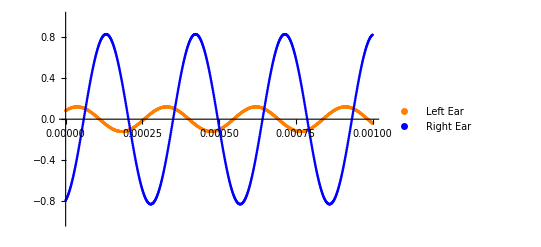

```mathematica
LeftEar ={#, Re[pfun[0.075,0.1]*Exp[I ω #]/.{ω->2 π Of}]}&/@Table[t, {t,0,0.001,0.001/1000}];
RightEar ={ #,Re[pfun[0.125,0.1]*Exp[I ω #]/.{ω->2 π Of}]}&/@Table[t, {t,0,0.001,0.001/1000}];
l1 = ListPlot[LeftEar,PlotLegends->{"Left Ear"},PlotStyle->{Orange}, PlotRange->{{0,0.001}, {-1,1}}];
l2 = ListPlot[RightEar,PlotLegends->{"Right Ear"},PlotStyle->{Blue},PlotRange->{{0,0.001}, {-1,1}}];
Show[l1,l2]
```

```mathematica
Max[#[[2]]&/@LeftEar]
```

0.120121

```mathematica
fm =NonlinearModelFit[LeftEar,a Sin[b x+c],{a,b,c},x,MaxIterations->Automatic, Method->NMinimize]
```

FittedModel[0.389661 Sin[0.0190325+9.56074 x]]

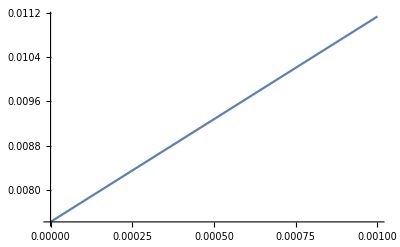

```mathematica
Plot[fm[x],{x,0,0.001}]
```

```mathematica
(*0.0022092735452950746Sin[0.998016746385263x+2.6597424066568682]*)
```

## Go again for PDE FREQUENCY DOMAIN : ( [Not Started]

## Functional Implementation of Single Plane 2D with Acoustics [Not Started]